Represent a graph as a list of it nodes, each node a list {m_i,{n_j1,n_j2,n_jN},ϕ_i}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,n_jN} the list of neighbors of node m; and ϕ_j the phase that determines if marbles are able to leave the node or not. When Sin[ω t+ϕ_i]≥ 0 marbles can leave the node.
Given a network, the rules of the simulation are that at every tick:
	■ Every node passes one of its marbles to one of its neighbors. The marble is passed if Sin[ω t+ϕ_i]≥ 0, otherwise the marble stays. The marble goes to one of the node’s neighbor with equal probability.

graphToNet[graph, fun] takes a graph (Mathematica style) and returns a list {{m_1,{n_11,n_12,n_(1 N_1)},ϕ_1},…,{m_i,{n_(j 1),n_(j 2),n_(j N_j)},ϕ_j},…,{m_N,{n_(N 1),n_(N 2),n_(N N_N)},ϕ_N}}; with N the number of nodes in the graph, n_(j s) the s-th neighbour of node j, m_j∈[1,N] an integer, and ϕ_j determined by fun.

```mathematica
graphToNet[g_Graph,ϕ_:(RandomChoice[{0,π/2}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],n=VertexCount[g]},
{RandomInteger[n],#,ϕ[]}&/@nei
]
```

netEvolve[graph, ω,T] takes a graph (represented as previously described), with N nodes, an integer T, and a real ω and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.

netEvolveTrace[graph, ω,T] does the same as netEvolve, but it returns a list {{{s_11,…,s_N1},…,{s_(1T),…,s_(N T)}}},E} with s_(n t) the number of the node that received the marble from node n at time t.

```mathematica
ω=1/2;
```

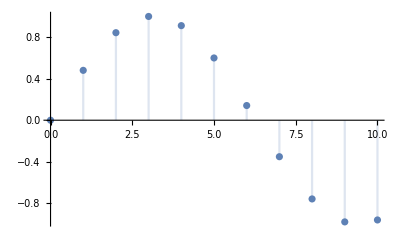

```mathematica
DiscretePlot[Sin[ω t], {t,0,10}]
```

```mathematica
remove[node:{0,neighs_,ϕ_}]:={node,0};
remove[node:{m_,neighs_,ϕ_}]:=If[Sin[ω t+ϕ]<0,{node,0},
{{m-1,neighs,ϕ},RandomChoice[neighs][[1]]}];
```

```mathematica
netEvolve[graph_List,ω_Real?Positive,T_Integer]:=Module[
{output=graph[[All,1]],nodes=Length[graph],add,remove,t,tmp},
remove[node:{0,neighs_,ϕ_}]:=node;
remove[node:{m_,neighs_,ϕ_}]:=If[Sin[ω t+ϕ]<0,node,{{m-1,neighs,ϕ},RandomChoice[neighs]}];
add=remove/@graph;
tmp=Select[add,{_List,i_}->i];



add=remove/@graph;
```

```mathematica
Clear[t]
```

```mathematica
NestWhileList[{#[[1]]+1,Sin[.2 #[[1]]]}&,{0,0},#[[1]]≤ 10&]
```

{{0,0},{1,0.},{2,0.198669},{3,0.389418},{4,0.564642},{5,0.717356},{6,0.841471},{7,0.932039},{8,0.98545},{9,0.999574},{10,0.973848},{11,0.909297}}

```mathematica
t
```

1